```mathematica
dat = Import["/Users/daria/OpticalAbsorptionTBG/model_bilayer_sigma/model_bilayer_energies_100_0.001.txt","Data"];
dat⟦1⟧⟦1⟧
```

-2.41056215748877278

```mathematica
Length@dat
```

40401

```mathematica
dat⟦1000⟧⟦2⟧
```

0.0817723905054544148

```mathematica
Num = 100;
table = Table[dat⟦(i+Num)*(2*Num+1)+(j+Num)⟧⟦2⟧,{i,-Num,Num,1},{j,-Num,Num,1}];
ListContourPlot[table]
```

Part::partd: Part specification List⟦2⟧ is longer than depth of object.

-Graphics-

```mathematica
Num = 100;
table = Table[dat⟦(i+Num)*(2*Num+1)+(j+Num)⟧⟦1⟧,{i,-Num,Num,1},{j,-Num,Num,1}];
ListContourPlot[table]
```

Part::partd: Part specification List⟦1⟧ is longer than depth of object.

-Graphics-

```mathematica
Num = 100;
table = Table[dat⟦(i+Num)*(2*Num+1)+(j+Num)⟧⟦3⟧,{i,-Num,Num,1},{j,-Num,Num,1}];
ListContourPlot[table]
```

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

-Graphics-

```mathematica
Num = 100;
table = Table[dat⟦(i+Num)*(2*Num+1)+(j+Num)⟧⟦4⟧,{i,-Num,Num,1},{j,-Num,Num,1}];
ListContourPlot[table]
```

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

-Graphics-

```mathematica
Num = 100;
projdat=dat[[Num;;-Num]];
Length@projdat
```

403

```mathematica
projdat⟦1⟧
```

{-1.66800003602867775,-1.26800003602867806,1.26800003602867739,1.66800003602867752}

```mathematica
projdat⟦2⟧
```

{-2.03530285651461629,-1.63530285651461593,1.63530285651461638,2.03530285651461673}

-1.66800003602867775

403

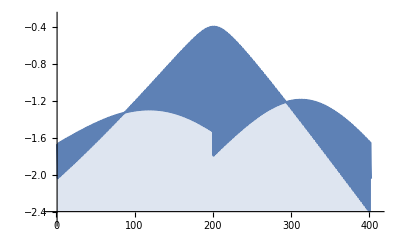

```mathematica
lowval = projdat⟦All,1⟧;
lowval⟦1⟧
Length@lowval
DiscretePlot[lowval⟦i⟧,{i,1,402}]
```